```mathematica
(*Vector potential A is only in the phi direction*)
(*Calculates the induced electric field strength E about a ring of current at a plane perpendicular to the ring distance z away.*)
Remove["Global`*"]
(*
a: radius of the ring,
x: distance from the axis of the ring,
u: permeability,
imax: amplitude of the current,
f: frequency,
t: phase*)
```

```mathematica
k = Sqrt[4*a*x/((x+a)^2+z^2)];i = imax*Cos[2Pi*f*t]
```

imax Cos[2 f π t]

```mathematica
A = (u*i*a)/(Pi*Sqrt[((x+a)^2+z^2)])*(((2-k^2)*EllipticK[k^2]-2*EllipticE[k^2])/k^2);
```

```mathematica
(*Change the values of a, z, imax, and f to calculate new values*)
```

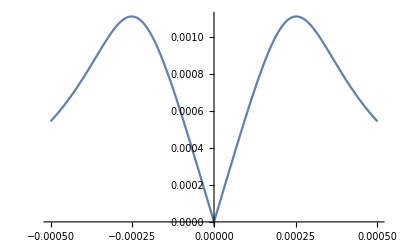

```mathematica
Plot[Abs[D[A,t]]/.{a -> 0.00025,z->0.00015,u->4*Pi*10^-7,imax->4,f->500,t->Pi/2},{x,-0.0005,0.0005}]
```

```mathematica
FindMaximum[Abs[D[A,t]]/.{a -> 0.00025,z->0.00015,u->4*Pi*10^-7,imax->4,f->500,t->Pi/2},{x,0.0005}]
```

{0.00111023,{x→0.000251765}}